```mathematica
nrealis=5;
ntemp=5;
nn=ntemp nrealis;
temDW=Developer`ToPackedArray[{0.05,0.06,0.2,0.35,0.5}];
tem=Developer`ToPackedArray[{0.35, 0.4, 0.45,0.5,0.55}];
eps=1;
candmoves=Developer`ToPackedArray[{-eps,0.,eps}];
xInit=ConstantArray[0.,{nn}];
tmp=(-1.)/Developer`ToPackedArray[Table[tem[[Quotient[i,nrealis]+1]],{i,0,nn-1}]];

f1[x_]:=Piecewise[{{-3*x,x<0},{-x^3*(1/2)^2/24+x,x>0}}]
f[x_]:=With [{ciccio = UnitStep[x]}, ciccio*(-x^3*(1/2)^2/24+x)+Subtract[1,ciccio]*-5*x]
g[x_]:=(x^2-1)*x^2
```

```mathematica
min=0;
time=0;
metaTime=ConstantArray[0,{nn}];
xOld=xInit;
(*enOld=With[{square=xOld xOld},((1/2)*square-1.)*(1/2) square];*)
enOld = f[xOld];
{{AbsoluteTiming[While[min==0,xNew=RandomChoice[candmoves,nn]+xOld;
enNew=f[xNew];
alfas=Exp[tmp Ramp[Subtract[enNew,enOld]]];
betas=RandomReal[{0.,1.},nn];
xOld=With[{λ=UnitStep[Subtract[alfas,betas]]},λ xNew+Subtract[1,λ] xOld];
enOld=With[{λ=UnitStep[Subtract[alfas,betas]]},λ enNew+Subtract[1,λ] enOld];
metaTime=With[{λ=UnitStep[-xOld+6],μ=Unitize[metaTime]},Subtract[1,λ] (μ metaTime+Subtract[1,μ] time)+λ metaTime];
min=Min[metaTime];
++time];]}, {□}}
```

{{{585.108,Null}},{□}}

```mathematica
metaTime;
```

```mathematica
Mean[Log[metaTime]] //N
Mean[metaTime]//N
Log[2148]//N
```

7.20438

2148.4

7.67229

```mathematica
1/5 (Log[139]+Log[959]+Log[3028]+Log[3149]+Log[3467])//N
```

7.20438

```mathematica
T1Res=metaTime[[1;;nrealis]];
T2Res=metaTime[[nrealis+1;;2*nrealis]];
T3Res=metaTime[[2*nrealis+1;;3*nrealis]];
T4Res=metaTime[[3*nrealis+1;;4*nrealis]];
T5Res=metaTime[[4*nrealis+1;;5*nrealis]];
LogT1Res=Log[T1Res];
LogT2Res=Log[T2Res];
LogT3Res=Log[T3Res];
LogT4Res=Log[T4Res];
LogT5Res=Log[T5Res];
(Mean[LogT1Res]-Mean[LogT2Res])/(1/tem[[1]]-1/tem[[2]])
```

3.58613

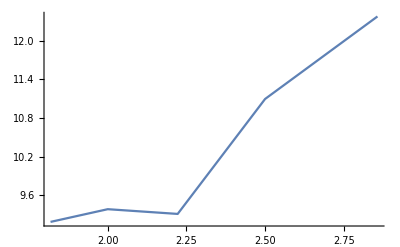

```mathematica
escapeTimes = {Mean[LogT1Res],Mean[LogT2Res],Mean[LogT3Res],Mean[LogT4Res],Mean[LogT5Res]};
ListLinePlot[Transpose[{1/tem,escapeTimes}]]
```

```mathematica
nrealis=1;
ntemp=5;
nn=ntemp nrealis;
temDW=Developer`ToPackedArray[{0.05,0.06,0.2,0.35,0.5}];
tem=Developer`ToPackedArray[{0.6, 0.7, 0.8,0.9,0.95}];
eps=1;
candmoves=Developer`ToPackedArray[{-eps,0.,eps}];
xInit=ConstantArray[0.,{nn}];
tmp=(-1.)/Developer`ToPackedArray[Table[tem[[Quotient[i,nrealis]+1]],{i,0,nn-1}]];

f1[x_]:=Piecewise[{{-3*x,x<0},{-x^3*(1/2)^2/24+x,x>0}}]
f[x_]:=With [{ciccio = UnitStep[x]}, ciccio*(-x^3*(1/2)^2/24+x)+Subtract[1,ciccio]*-5*x]
g[x_]:=(x^2-1)*x^2
```

```mathematica
min=0;
time=0;
metaTime=ConstantArray[0,{nn}];
xOld=xInit;
(*enOld=With[{square=xOld xOld},((1/2)*square-1.)*(1/2) square];*)
enOld = f[xOld];
{{AbsoluteTiming[
Module [{enNew, enOld, alfas, betas, xOld},xOld = xInit;enOld = f[xOld]; While[min==0,xNew=RandomChoice[candmoves,nn]+xOld;
enNew=f[xNew];
alfas=Exp[tmp Ramp[Subtract[enNew,enOld]]];
betas=RandomReal[{0.,1.},nn];
xOld=With[{λ=UnitStep[Subtract[alfas,betas]]},λ xNew+Subtract[1,λ] xOld];
enOld=With[{λ=UnitStep[Subtract[alfas,betas]]},λ enNew+Subtract[1,λ] enOld];
metaTime=With[{λ=UnitStep[-xOld+6],μ=Unitize[metaTime]},Subtract[1,λ] (μ metaTime+Subtract[1,μ] time)+λ metaTime];
min=Min[metaTime];
++time] ];
]}, {□}}
```

{{{0.352647,Null}},{□}}

```mathematica
metaTime
```

{139,3028,3467,3149,959}